## .08.08

## Dodelson 8.6

### Exercise 6. Obtain a semianalytic solution for Θ_0+Ψ and Θ_1 at recombination by carrying out the integrals Eq.8.24 and .8.26.

```mathematica
<<Dodelson`ChangeVariable`
<<Dodelson`Definitions`
<<Dodelson`CommonParameters`
SoundSubs;
EnergyDenSubs;
equalitySubs;
ayetaSubs
RecombinationSubs;
```

x::shdw: Symbol TraditionalForm`"x" appears in multiple contexts TraditionalForm`{"Definitions`", "Global`"}; definitions in context TraditionalForm`"Definitions`" may shadow or be shadowed by other definitions.

c::shdw: Symbol TraditionalForm`"c" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Global`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

H::shdw: Symbol TraditionalForm`"H" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

a::shdw: Symbol TraditionalForm`"a" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

k::shdw: Symbol TraditionalForm`"k" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

x::shdw: Symbol TraditionalForm`"x" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`", "Global`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

T::shdw: Symbol TraditionalForm`"T" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

defR ::  R(a_):=(3 ρ_m(a))/(4 ρ_γ(a))

defReta :: R_η(η_):=R(a)/.a→y(η) a_eq/.subC

Eqn819 ::  c_s(a_):=√(1/(3 (R(a)+1)))

Eqn819eta ::  c_s(eta_):=√(1/(3 (R_η(eta)+1)))

Eqn822 ::  r_s(η$_):=∫_0^η$ c_s(eta$175)ⅆeta$175

defRhoGR ::  ρ_γ(a_):=(C_γ (1/a)^4 ρ_cr)/h^2

defRhoM ::  ρ_m(a_):=(Ω_m ρ_cr)/a^3

defRhoCR ::  ρ_cr:=(3 H_0^2)/(8 π G)

Some definitions referencing 'equality' point :

defkeq :: k_eq→H(a_eq) a_eq

subkeq :: k_eq→√2 √((H_0^2 Ω_m)/a_eq)

subH0 :: H_0→(√((a_eq k_eq^2)/Ω_m))/(√2)

subkkeq :: k→k_eq kk_eq

subetat :: η'(t)→1/(a(η))

subyeta :: y(η)→(a(η))/a_eq

subDyeta :: y'(η)→(a'(η))/a_eq

subHt :: H→(a'(t))/(a(t))

defaeta :: a(η_):=y(η) a_eq

subHeta :: H→(a'(η))/(a(η))^2

defRhoGR ::  ρ_γ(a_):=(C_γ (1/a)^4 ρ_cr)/h^2

defRhoM ::  ρ_m(a_):=(Ω_m ρ_cr)/a^3

defRhoCR ::  ρ_cr:=(3 H_0^2)/(8 π G)

subaeq :: a_eq→C_γ/(h^2 Ω_m)

subC :: C_γ→h^2 a_eq Ω_m

η[a] = (2 √2 (√(h^2 (a+a_eq) Ω_m)-h √a_eq √Ω_m))/(h √a_eq k_eq √Ω_m)

η_y[y = a/a_eq] = (2 √2 (√(y+1)-1))/k_eq

Jacobian dη/dy => (√2)/(√(y+1) k_eq)
Or  -> dη/dy = (√a_eq)/(√(y+1) H_0 √Ω_m)

y[η] = 1/8 η k_eq (η k_eq+4 √2)

subZrecomb :: z_*→1000

subarecomb :: a_*→1/(z_*+1)

subyrecomb :: y_*→(a_*)/a_eq

With : r_s(η$_):=∫_0^η$ c_s(eta$175)ⅆeta$175 => (1.88562 sinh^-1(0.612372 η k_eq+1.73205)-2.48328)/k_eq

The integrand of Eqn.8.24 using rs as the equation parameter and rs1 as the integration variable : {0.5 kkeq cosh(3.57095×10^-17 (1.48512×10^16 rs1 k_eq+3.68797×10^16)) sin(kkeq (rs-rs1) k_eq) k_eq (Φ_y(kkeq,1/8 eta(rs1) k_eq (eta(rs1) k_eq+4 √2))-Ψ_y(kkeq,1/8 eta(rs1) k_eq (eta(rs1) k_eq+4 √2)))}

What are the values of eta0, k, eta*, for Fig. 8.6 and the ranges of eta and rs[eta]?

The equality value of η_* = 4.424×10^16 and  rs_* = 2.40504×10^16
The present day value of η_0 = 2.16942×10^18 and  rs0 = 3.79194×10^17

For Fig.8.6 : k η_0 ranges to : 2000 or k ranges from 0 to 9.21905×10^-16
The value of k_eq is : 1.06549×10^-17
So kkeq ranges from 0 to {0,86.524}
and η_* k_eq = 0.471373

Plot k^(3/2)|Cos[k rs[η_*]]| to verify units used. Cos[k rs[η_*]] > Cos[k rs[eta_*]] > Cos[k rsstar] {k,0,2000/η_0} ⇒ Cos[keta/η_0 rsstar]{keta,0,2000}

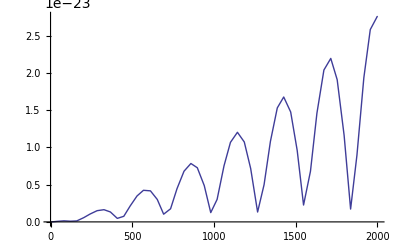

This plot varies from Fig.8.6 by : 
wavelength is longer by factor of 1.8<<look at rs,
the amplitude differs considerably <<look near k==0.

Check units in Mpc : keq = 0.00109589
r_s[η_0] = 3686.75
r_s[η_*] = 233.832

k_eq (2.44647×10^32 k_eq+3.12824×10^16)

0.361085

What does the integrand look like?

1/(√3)kkeq sin(kkeq (1.88562 sinh^-1(0.612372 η k_eq+1.73205)-1.88562 sinh^-1(0.612372 k_eq η_1+1.73205)+0.)) k_eq (Φ_y(kkeq,1/8 k_eq η_1 (k_eq η_1+4 √2))-Ψ_y(kkeq,1/8 k_eq η_1 (k_eq η_1+4 √2)))

```mathematica
Clear[Φ,Ψ]
Eqn824:=Module[{},holdint824=HoldForm[
integrand824[η_,eta_,kkeq_]:=(kkeq Subscript[k, eq])/(√3)(Φ[kkeq,eta]-Ψ[kkeq,eta]) Sin[Subscript[k, eq] kkeq( Subscript[r, s][η]-Subscript[r, s][eta])]
];
holdint824rs=HoldForm[
integrand824rs[rs_,rs1_,kkeq_]:=(kkeq Subscript[k, eq])/(√3)(Φ[kkeq,eta[rs1]]-Ψ[kkeq,eta[rs1]]) Sin[Subscript[k, eq] kkeq( rs-rs1)]
];
hold824=HoldForm[
Subscript[Θ, 0][η]+Φ[η] == (Subscript[Θ, 0][0]+Φ[0])Cos[Subscript[k, eq] kkeq  Subscript[r, s][η]] + ∫_0^η integrand824[η,eta,kkeq]ⅆeta
];
hold824rs=HoldForm[
Subscript[Θ, 0][eta[rs]]+Φ[eta[rs]] == (Subscript[Θ, 0][0]+Φ[0])Cos[Subscript[k, eq] kkeq  rs] + ∫_0^rs integrand824rs[rs,rs1,kkeq]detadrs ⅆrs1
];
];
Eqn824;
e824=ReleaseHold[hold824];
ReleaseHold[holdint824];

Φ[kkeq_,η_]:=Subscript[Φ, y][kkeq,y[η] ]
Ψ[kkeq_,η_]:=Subscript[Ψ, y][kkeq,y[η] ]
integrand824[η,Subscript[η, 1],kkeq];

(ReleaseHold[#]&)/@{defReta,defR,Eqn819eta,Eqn822};
cseta=Subscript[c, s][eta]//FullSimplify;
rstmp=Integrate[cseta,{eta,0,eta1},Assumptions->Element[eta1,Reals]&&Element[Subscript[k, eq],Reals]&&eta1>0&&Subscript[k, eq]>0
];
Subscript[r, s][η_]:=rstmp/.eta1->η;
Print["With : ",Eqn822," => ",Subscript[r, s][η]];
etaP[rs_]:=eta1/.Solve[rstmp==rs,eta1]
detadrs=D[etaP[rs1],rs1];
Clear[eta,h];

integrand824[η,Subscript[η, 1],kkeq]//Simplify;
tmp=%//PowerExpand//FullSimplify;
(ReleaseHold[#]&)/@{holdint824rs};
holdint824rs;
Print["The integrand of Eqn.8.24 using rs as the equation parameter and rs1 as the integration variable : ",
integrand824rs[rs,rs1,kkeq] detadrs
]
Print["What are the values of eta0, k, eta*, for Fig. 8.6 and the ranges of eta and rs[eta]? "]
h=.5;
Subscript[Ω, m]=.015/h^2;
Print["The equality value of η_* = ",
tmp=Subscript[η, y][SubStar[y]]/.subyrecomb/.subarecomb/.subZrecomb/.subkeq;
SubStar[η]=tmp//NumericalValues," and  rs_* = ",
rsstar=Subscript[r, s][SubStar[η]]/.subkeq//NumericalValues,"
The present day value of η_0 = ",
tmp=Subscript[η, y][.23/Subscript[a, eq]]/.subyrecomb/.subarecomb/.subZrecomb/.subkeq (*XXXX .23 should be 1 *);
Subscript[η, 0]=tmp//NumericalValues," and  rs0 = ",
rs0=Subscript[r, s][Subscript[η, 0]]/.subkeq//NumericalValues
]
Print["For Fig.8.6 : k η_0 ranges to : ",2000," or k ranges from 0 to ",2000/Subscript[η, 0],"
The value of k_eq is : ",(keq=Subscript[k, eq]/.subkeq//NumericalValues),"
So kkeq ranges from 0 to ",rangekkeq={0,2000/Subscript[η, 0]/keq},"
and η_* k_eq = ",SubStar[η] keq
]

Print["Plot k^(3/2)|Cos[k rs[η_*]]| to verify units used.",
" Cos[k rs[η_*]] > Cos[k rs[eta_*]] > Cos[k rsstar] {k,0,2000/η_0} ⇒ Cos[keta/η_0 rsstar]{keta,0,2000}"
]
Plot[ (keta0/Subscript[η, 0])^(3/2) Abs[Cos[(keta0/Subscript[η, 0]) rsstar]],{keta0,0,2000}]
Print["This plot varies from Fig.8.6 by : 
wavelength is longer by factor of 1.8<<look at rs,
the amplitude differs considerably <<look near k==0."];

Print["Check units in Mpc : keq = ",keq/sec2Mpc//NumericalValues,"
r_s[η_0] = ",Subscript[r, s][η]sec2Mpc/.subkeq/.η->Subscript[η, 0]//NumericalValues,"
r_s[η_*] = ",Subscript[r, s][η]sec2Mpc/.subkeq/.η->SubStar[η]//NumericalValues
]
y[SubStar[η]]
%/.subkeq//NumericalValues
Print["What does the integrand look like? "]
in=integrand824[η,Subscript[η, 1],kkeq]//Simplify
```

```mathematica
in1=in/.subkeq/.Subscript[η, 1]->eta1/.η->Subscript[η, 0]/.eta1->SubStar[η]//NumericalValues
```

6.15161×10^-18 kkeq sin(3.78402 kkeq) (Φ_y(kkeq,0.361085)-Ψ_y(kkeq,0.361085))

Φ(0)

(1 | 0.994157
2 | 0.999379
3 | 0.999938
4 | 0.999734
5 | 0.710543
6 | 355.271
7 | 0.
8 | 3.55271×10^8
9 | 0.
10 | 0.)

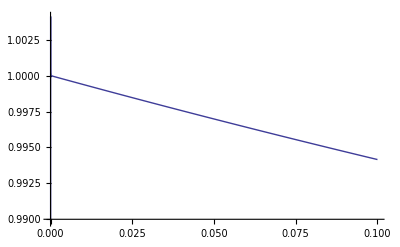

```mathematica
Subscript[Φ, y][kkeq_,y_]:=Φbar[kkeq,y]((1-T[kkeq])ⅇ^(-.11(y kkeq)^1.6)+T[kkeq])
Subscript[Ψ, y][kkeq_,y_]:=Ψbar[kkeq,y]((1-T[kkeq])ⅇ^(-.097( y kkeq)^1.6)+T[kkeq])
T[kkeq_]:=Log[1+.171 kkeq]/(.171 kkeq)(1+.284 kkeq+(1.18 kkeq)^2+(.399 kkeq)^3+(.49 kkeq)^4)^(-.25)
Φbar[kkeq_,y_]:=3/4(1/kkeq)^2(y+1)/y^2 Subscript[Δ, T][y]
Ψbar[kkeq_,y_]:=-3/4(1/kkeq)^2(y+1)/y^2(Subscript[Δ, T][y]+.65 N2[y]/(1+y))
N2[y_]:=-0.1(20 y +19)/(3 y +4)y^2/(y+1)Φls[y]-8/3 y/(3 y +4)+8/9 Log[3 y/4+1]
Subscript[Δ, T][y_]:=(1.16-(.48 y)/(y+1))Φls[y] y^2/(y+1)
Φls[y_]:=Φ[0]/10 1/y^3(16 √(1+y)+9 y^3+2 y^2-8 y-16)
Limit[Φls[y],y->0]
Table[{i,Φls[10^-i]/Φ[0]//N},{i,1,10}]
Plot[Φls[y]/Φ[0],{y,10^-10,10^-1}]
```

```mathematica
Φ[0]:=10^-6;
xkkeq=1;
in/.subkeq/.Subscript[η, 1]->eta1/.η->Subscript[η, 0]/.kkeq->xkkeq//Simplify;
in1=%//NumericalValues;

ni=200;
etamin=10^-20 SubStar[η]
list=Table[{xeta=i etamin 10^1/ni + etamin, 
in1/.eta1->xeta//NumericalValues},
{i,0,ni}];
ListLinePlot[list,PlotRange->All]
in2=in1//NumericalValues;
list=Table[{xeta=i Subscript[η, 0]/ni + etamin,
NIntegrate[in2,{eta1,etamin,xeta},Method->"LocalAdaptive",MaxRecursion->100]},
{i,1,ni}];
ListLinePlot[list,PlotRange->All]
```

0.0004424

-Graphics-

-Graphics-

```mathematica
integrand824[.1,.2,.3]//Simplify
%/.NumericalValues[subkeq]
```

```mathematica
Print["Problem specific values ==> "]
Subscript[C, γ]=2.47 10^-5;
Subscript[C, ν]=1.68 10^-5;
Print["Coefficient for radiation energy term -> ",
subCval=C->(Subscript[C, γ]+Subscript[C, ν])]
tmp=aeq/.subaeq/.subCval/.Subscript[Ω, b]->.015/h^2;
Print["a_eq for h^2Ω_b = .015  -> ",xaeq0=tmp ]

keq/.subkeq/.Subscript[a, eq]->aeq/.subaeq/.Subscript[H, 0]->h 1.023 10^-10 (*   year^-1   *);
%/(365*24*3600)       (*  sec^-1 *)  ;
%[[1]] (3.0856 10^24)/(3 10^10)       (*  Mpc  *)   ;
%/.subCval;
xkeqInvMpc=%/.Subscript[Ω, b]->.015/h^2;
subkeqVal=keq->xkeqInvMpc;
Print["k_eq(Mpc^-1) = ",subkeqVal ];
Print["What is η_0[y]  now  ≡ (a=1) ?  -> ",etay ]
Print["Or  at  a = 1 -> ",
eta0=etay/.y->1/aeq/.subHkeq//PowerExpand]
eta0Mpc=eta0/.subkeqVal/.aeq->xaeq0;
Print["Now    η_0(Mpc) = ",eta0Mpc  ];
Print["At recombination a_* = ",SubStar[a]," ;  y_* = ",SubStar[y]=SubStar[a]/xaeq0]
Print["and η at recombination, η_* -> ",etaystar=etay/.y->SubStar[y]/.subHkeq/.subkeqVal//PowerExpand ]
```

```mathematica
Print["Now Compute Eqn 8.22,  r_s[y] with c_sintegrand = ",Subscript[cc, s][y] detadyy ];
rs=Integrate[Subscript[cc, s][y] detadyy,{y,0,ya},Assumptions->Re[ya]≥0];
rsy=rs/.ya->y;
Print["r_s[y=a/a_eq] = ",rsy]
rsx = rsy/.y->x;

Print["r_s[y_*] = ", rsy/.y->SubStar[y]];

Clear[T,c,r,R,Φ,Ψ,Θ]
η[z_]:=etay/.y->z;
detadyx=detadyy/.y->x ;
sinterm= Sin[k(rsy-rsx)];
sinterm=sinterm//FullSimplify;
integrand824[kkeq_,x_]:=kkeq keq  (Φ[kkeq,x]-Ψ[kkeq,x])sinterm  detadyx
(*----------------*)
Print["The integrand[x] of Eqn.824 is ",
integrand824[kkeq,x]
]
```

```mathematica
eqn824[kkeq_,y_]:=(Subscript[Θ, 0][0]+Φ[0])Cos[keq kkeq rsy]+1/(√3)∫_0^y integrand824[kkeq,x] ⅆx
Print["Eqn 824 in terms of k/k_eq=kkeq    and    {x,y}∼a/a_eq => ",
eqn824[kkeq,y]]
eqn824N[kkeq_,y_]:=(Subscript[Θ, 0][0]+Φ[0])Cos[keq kkeq rsy]+1/(√3)NIntegrate[integrand824[kkeq,x],{x,0,y}]
(****************)
(* kkeq = k/keq *)
Clear[Φls]
Φ[kkeq_,y_]:=Φbar[kkeq,y]((1-T[kkeq])ⅇ^(-.11(y kkeq)^1.6)+T[kkeq])
Ψ[kkeq_,y_]:=Ψbar[kkeq,y]((1-T[kkeq])ⅇ^(-.097( y kkeq)^1.6)+T[kkeq])
T[kkeq_]:=Log[1+.171 kkeq]/(.171 kkeq)(1+.284 kkeq+(1.18 kkeq)^2+(.399 kkeq)^3+(.49 kkeq)^4)^(-.25)
Φbar[kkeq_,y_]:=3/4(1/kkeq)^2(y+1)/y^2 Subscript[Δ, T][y]
Ψbar[kkeq_,y_]:=-3/4(1/kkeq)^2(y+1)/y^2(Subscript[Δ, T][y]+.65 N2[y]/(1+y))
N2[y_]:=-0.1(20 y +19)/(3 y +4)y^2/(y+1)Φls[y]-8/3 y/(3 y +4)+8/9 Log[3 y/4+1]
Subscript[Δ, T][y_]:=(1.16-(.48 y)/(y+1))Φls[y] y^2/(y+1)
Φls[y_]:=Φ[0]/10 1/y^3(16 √(1+y)+9 y^3+2 y^2-8 y-16)
```

```mathematica
Clear[kkeq,x,keq];
Print["Test integrand Limits x->0.  By doing PowerExpand and Simplify the simplified expression produced does not have a convergent limit x->0; whereas, the unSimplified limit does.  Is there a bug in Mathematica? "]

intg=integrand824[kkeq,x]/.k->keq kkeq;

Print["The x->0 limit of the unSimplified integrand is ",
Limit[intg,x->0]//Expand//Apart//Simplify,"
So there might not be a non-convergent integral problem.
=============================================="
]
```

```mathematica
Print["There are unstable numerical problems with the integrand near x -> 0.  So we attempt to combine a polynomial approximation of the integrand near x=0 with the original."]

Phi0=10^-6;
Theta0=Phi0;
Xmin=.00001;
Xmax=.1;
minkkeq = .00001;
maxkkeq=4000;
Xintvar=Xmin;
Xaeq=0.002766666666666667;
Xystar=.36;

tmpSeries=Series[intg,{kkeq,0,3},{x,0,3}]//Normal;
tmpSeries=tmpSeries/.Φ[0]->Phi0/.y->Xystar //Simplify;

Print["Series approximation"]
Plot3D[tmpSeries,{x,Xmin,Xmax},{kkeq,minkkeq,maxkkeq}]
Print["Series approximation"]
Print["Series approximation along x = ",Xmin]
Plot[tmpSeries/.x->Xmin,{kkeq,minkkeq,maxkkeq}]

tmp=intg;
tmp=tmp/.Φ[0]->Phi0/.y->Xystar //Simplify;
Print["Full integrand"]
Plot3D[tmp,{x,Xmin,Xmax},{kkeq,minkkeq,maxkkeq}]
Print["Full integrand along x = ",Xmin]
Plot[tmp/.x->Xmin,{kkeq,minkkeq,maxkkeq}]

Print["Full-Series difference"]
Plot3D[tmp-tmpSeries,{x,Xmin,Xmax},{kkeq,minkkeq,maxkkeq}]
Print["Full-Series difference along x = ",Xmin ]
Plot[tmp-tmpSeries/.x->Xmin,{kkeq,minkkeq,maxkkeq}]

intgz[xintvar_,xkkeq_,xaeq_,xylim_]:=intg/.kkeq->xkkeq/.aeq->xaeq/.y->xylim/.x->xintvar/.Φ[0]->Phi0/.Subscript[Θ, 0][0]->Theta0/.keq->xkeqInvMpc;

intgz[Xmin,maxkkeq,Xaeq,Xystar] //Simplify
intgz[xintvar_,xkkeq_,xaeq_,xylim_]:=tmpSeries/.kkeq->xkkeq/.aeq->xaeq/.y->xylim/.x->xintvar/.Φ[0]->Phi0/.Subscript[Θ, 0][0]->Theta0/.keq->xkeqInvMpc;
intgz[Xmin,maxkkeq,Xaeq,Xystar] //Simplify

intgZZ[xintvar_,xkkeq_,xaeq_,xylim_]:=Module[{tmp},
If[xintvar<0.0004 && xkkeq <10,tmp=tmpSeries/.kkeq->xkkeq/.aeq->xaeq/.y->xylim/.x->xintvar/.Φ[0]->Phi0/.Subscript[Θ, 0][0]->Theta0/.keq->xkeqInvMpc,
tmp=intg/.kkeq->xkkeq/.aeq->xaeq/.y->xylim/.x->xintvar/.Φ[0]->Phi0/.Subscript[Θ, 0][0]->Theta0/.keq->xkeqInvMpc];
tmp
]

intgZ0[xintvar_,xkkeq_,xaeq_,xylim_]:=Module[{tmp},
tmp=intg/.kkeq->xkkeq/.aeq->xaeq/.y->xylim/.x->xintvar/.Φ[0]->Phi0/.Subscript[Θ, 0][0]->Theta0/.keq->xkeqInvMpc
]

Print["Hybrid Integrand"]
Plot3D[intgZZ[x,kkeq,Xaeq,Xystar] ,{x,Xmin,Xmax},{kkeq,minkkeq,maxkkeq},ViewPoint->{-2.3,1.4,2}]
Print["Hybrid-Full Integrand"]
Plot3D[intgZZ[x,kkeq,Xaeq,Xystar] -intgZ0[x,kkeq,Xaeq,Xystar],{x,Xmin,Xmax},{kkeq,minkkeq,maxkkeq},ViewPoint->{-2.3,1.4,2}]

Print["Full Integrand"]
Plot3D[intgZ0[x,kkeq,Xaeq,Xystar],{x,Xmin,Xmax},{kkeq,minkkeq,maxkkeq},ViewPoint->{-2.3,1.4,2}]

Null
```

```mathematica
eqn824[kkeq_,xaeq_,xy_]:=Module[{tmp,sub,zz,tmpXX },
sub={aeq->xaeq,Φ[0]->Phi0,Subscript[Θ, 0][0]->Theta0,keq->xkeqInvMpc,y->xy};
tmp=(Subscript[Θ, 0][0]+Φ[0])Cos[keq kkeq rsy]/.sub;
tmpXX=
1/(√3)NIntegrate[intgZ0[zz,Max[kkeq,minkkeq],xaeq,xy]/.sub ,{zz,Xmin,xy}];
Print["kkeq = ",kkeq,"     xaeq = ",xaeq,"  xy = ",xy,"  tmpXX = ",tmpXX,"tmp= ",tmp];
tmp+=tmpXX;
tmp]

Phi0=10^-6;
Theta0=Phi0;
keta0[k_]:=1000 k  +minkkeq
Do[
{Print[{keta0[k],eqn824[(k+minkkeq)/xkeqInvMpc,xaeq0,SubStar[y]] } ],
Print[Φ[keta0[k],Xmin]]},{k,0,1}]
tmp=Limit[Φ[kkeq,y],{y->0}]
Print["There are a number of inconsistencies -> When we take the limit of y->0 or η->0 of Φ[kkeq,y] we do not get Φ[0] but -> ",tmp];
Limit[Φ[kkeq,y],{kkeq->0}]
Limit[%,{y->0}]
rsy/.y->0//PowerExpand//Simplify
%//FullSimplify
```